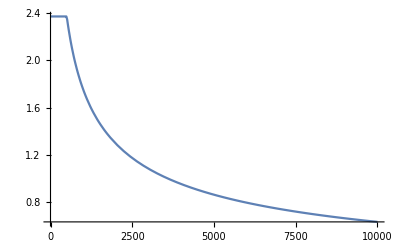

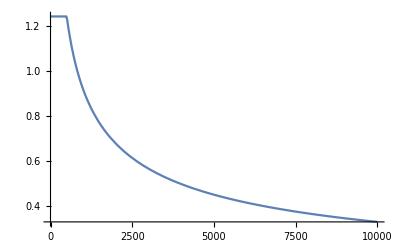

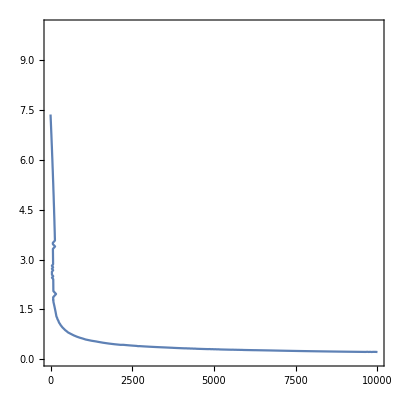

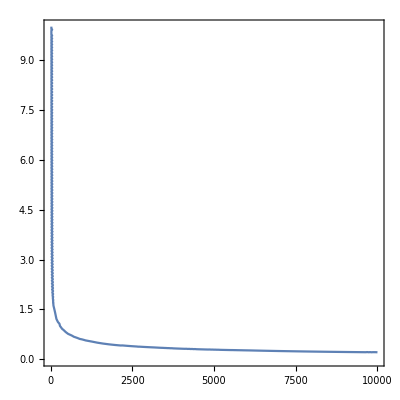

```mathematica
a=Plot[Sqrt[8/N*Log[4*(2*N)^50/.05]],{N,1,10000}]
b=Plot[Sqrt[2*Log[2*N*N^50]/N]+Sqrt[2/N*Log[1/0.05]]+1/N,{N,1,10000}]
c=ContourPlot[y^2==1/x*(2*y+Log[6*(2*x)^50/.05]),{x,1,10000}, {y,0,10}]
d=ContourPlot[y^2==1/(2*x)*(4*y*(1+y)+Log[4*x^100/.05]),{x,1,10000}, {y,0,10}]
```

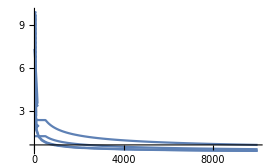

```mathematica
Show[a,b,c,d, PlotRange->All]
```

```mathematica
50
       8         (2 10000)
Sqrt[----- Log[4 -----------]]
     10000          0.05
```

0.632175

```mathematica
50
       Log[2 10000 10000  ]           2        1         1
Sqrt[2 --------------------] + Sqrt[----- Log[----]] + -----
              10000                 10000     0.05     10000
```

0.331309

```mathematica
50
        2      1                (2 10000)
NSolve[y  == ----- (2 y + Log[6 -----------]), y, Reals]
             10000                 0.05
```

{{y→-0.223498},{y→0.223698}}

```mathematica
100
        2       1                         10000
NSolve[y  == ------- (4 y (1 + y) + Log[4 --------]), y, Reals]
             2 10000                        0.05
```

{{y→-0.215028009800245069},{y→0.21522804980824667}}

```mathematica
2 5
     8       2
Sqrt[- Log[4 ----]]
     5       0.05
```

4.2546

```mathematica
5
       Log[2 5 2 ]         2      1       1
Sqrt[2 -----------] + Sqrt[- Log[----]] + -
            5              5     0.05     5
```

2.81365

```mathematica
2 5
        2    1              2
NSolve[y  == - (2 y + Log[6 ----]), y, Reals]
             5              0.05
```

{{y→-1.34395},{y→1.74395}}

```mathematica
2
                                       5
        2     1                       2
NSolve[y  == --- (4 y (1 + y) + Log[4 ----]), y, Reals]
             2 5                      0.05
```

{{y→-1.59787},{y→2.26454}}